Let' s start by exploring the functions that we’ll often rely on to do the “heavy lifting” in our simulations

If x^3 - 8 == 0,

the roots are: {{x→2},{x→-2 (-1)^(1/3)},{x→2 (-1)^(2/3)}}

or, if you prefer:  {{x→2.},{x→-1.-1.73205 ⅈ},{x→-1.+1.73205 ⅈ}}

Now let's try to solve: Cos[x]-x Sin[x]==0

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Note the warning!  The solution is not analytic.

You can silence warnings by tacking //Quiet on the

end of Solve[], but it's usually wiser to heed them.

In this case, Solve[] returned: Solve[{Cos[x]-x Sin[x]==0},x]

When Mathematica can't find an analytic solution,

the best answer is usually to repeat the question!

NSolve[] looks for an approximate numerical solution

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

Note the same warning!

NSolve[] returns: NSolve[{Cos[x]-x Sin[x]==0},x]

Of course, you can always estimate roots the old-fashioned way!

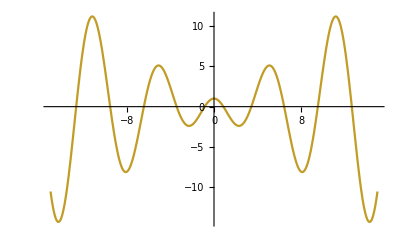

You can better your estimate using FindRoot:

We'll start our (Newton's Method) search around x=x0

If we start at x0=2.5, FindRoot[] returns:  {x→3.42562}

If we start at x0=9, FindRoot[] returns:  {x→9.52933}

If we start at x0=11, FindRoot[] returns:  {x→6.4373}

Hmmmm - the answer doesn't always converge to the closest root!

```mathematica
Remove["Global`*"]

(*************************************************************************)
(* Solve[] solves systems of algebraic equations *)

(* We'll store our system of equations in eqnlist *)
eqnlist = { x^3 - 8 == 0};

(* the syntax for Solve[] is pretty straightforward *)
soln = Solve[eqnlist,x];

Print["\nIf x^3 - 8 == 0,"]
Print["the roots are: " , soln]
Print["or, if you prefer:  ", soln//N]

(* Note that the outer list contains a list of single-element lists *)
(* each interior list containing one solution to the system of equations *)

(*************************************************************************)
(* Let's try something trickier... How about: *)
eqnlist={Cos[x]-x Sin[x]==0};

Print["\n\nNow let's try to solve: Cos[x]-x Sin[x]==0"]

soln = Solve[eqnlist,x];
Print["Note the warning!  The solution is not analytic."]
Print["\nYou can silence warnings by tacking //Quiet on the"]
Print["end of Solve[], but it's usually wiser to heed them."]


Print["\nIn this case, Solve[] returned: ",soln]

Print["\nWhen Mathematica can't find an analytic solution,"]
Print["the best answer is usually to repeat the question!"]

(* NSolve looks for an approximate numerical solution *)
Print["\nNSolve[] looks for an approximate numerical solution"]
soln= NSolve[eqnlist,x];

Print["Note the same warning!"]
Print["NSolve[] returns: ",soln]

(* The problem is, NSolve tries to solve the system of *)
(* equations first, then use the result to find a numerical *)
(* approximation...  if it can't solve the system....... *)

Print["\n\nOf course, you can always estimate roots the old-fashioned way!"]

Plot[Cos[x]-x Sin[x],{x,-15,15}]

Print["\nYou can better your estimate using FindRoot:"]
Print["We'll start our (Newton's Method) search around x=x0"]
root[x0_] := FindRoot[eqnlist,{x,x0}];  (* why the delayed assignment?? *)

Print["If we start at x0=2.5, FindRoot[] returns:  ",root[2.5]]
Print["If we start at x0=9, FindRoot[] returns:  ",root[9]]
Print["If we start at x0=11, FindRoot[] returns:  ",root[11]]

Print["Hmmmm - the answer doesn't always converge to the closest root!"]
```

More often than not, we' ll be called upon to solve systems with differential equations ...

The solution to the system: {ω0^2 x[t]+x''[t]==0} looks like...

{x[t]→C[1] Cos[t ω0]+C[2] Sin[t ω0]}

(Note the undetermined constants!)

Now add some initial conditions to resolve those constants.

The solution to the system: {ω0^2 x[t]+x''[t]==0,x[0]==A,x'[0]==0} looks like...

{x[t]→A Cos[t ω0]}

What if there is no analytic solution?  Consider a simple pendulum

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

Part::partw: Part 1 of {} does not exist.

The solution to the system: {ω0^2 Sin[x[t]]+x''[t]==0,x[0]==A,x'[0]==0} looks like...

{}⟦1⟧

I guess I'm not really surprised...

We can use NDSolve to obtain a NUMERICAL solution

NDSolve[] returns:  {x→InterpolatingFunction[…]}

NDSolve returns an interpolation table - let's put it to use!

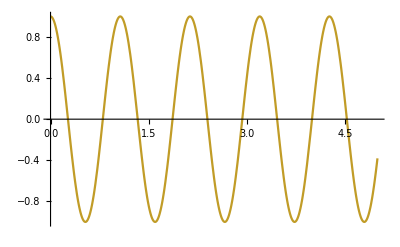

What if we over-run the domain of the interpolation table?

Short answer - make sure you don't!

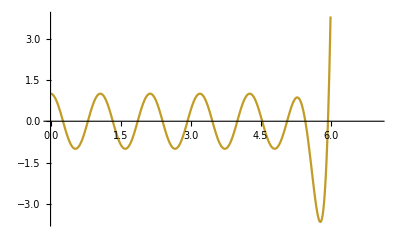

```mathematica
Remove["Global`*"]

(*************************************************************************)
(* We'll start simple *)

(* make sure the add [t] to all the (x)'s, (x')'s, (x'')'s... and so on! *)
eqnlist = {x''[t] + ω0^2 x[t]==0};

(* The sytax is mostly obvious - we're solving for the function x[t] *)
(* over the parameter t *)
soln=DSolve[eqnlist,x[t],t][[1]];   (* Important: What does the [[1]] do? *)

Print["The solution to the system: ",eqnlist," looks like..."]
Print[soln]
Print["(Note the undetermined constants!)"]

(*************************************************************************)
Print["\nNow add some initial conditions to resolve those constants."]
eqnlist = {x''[t] + ω0^2 x[t]==0,x[0]==A,x'[0]==0};
soln=DSolve[eqnlist,x[t],t][[1]];

Print["The solution to the system: ",eqnlist," looks like..."]
Print[soln]

(*************************************************************************)
Print["\nWhat if there is no analytic solution?  Consider a simple pendulum"]

eqnlist={x''[t] + ω0^2 Sin[x[t]]==0,x[0]==A,x'[0]==0};
soln=DSolve[eqnlist,x[t],t][[1]];

Print["The solution to the system: ",eqnlist," looks like..."]
Print[soln]
Print["I guess I'm not really surprised..."]

(*************************************************************************)
Print["\n\nWe can use NDSolve to obtain a NUMERICAL solution"]

(* Same diff eq, copied for convenience *)
eqnlist={x''[t] + ω0^2 Sin[x[t]]==0,x[0]==A,x'[0]==0};

(* But we'll need numbers to start! *)
A = 1;
ω0 = 2 π;

tlo = 0;
thi=5;

(* A few important observations *)
(* We are solving for x, not x[t] in NDSolve. *) 
(* Note that we still use x[t] in the diff eq! *)
(* The parameter (t) is given with the range *)
(* of values the numerical approximation is to *)
(* be taken over *)

soln=NDSolve[eqnlist,x,{t,tlo,thi}][[1]];     (* there's that [[1]] again! *)
Print["NDSolve[] returns:  ",soln]  

Print["NDSolve returns an interpolation table - let's put it to use!\n"]

Plot[x[t]/.soln,{t,tlo,thi}]     (* Not bad...  *)

Print["\nWhat if we over-run the domain of the interpolation table?"]
Print["Short answer - make sure you don't!"]
Plot[x[t]/.soln,{t,tlo,thi+2}]
```

Finally - let’s finish that oscillator example we started!  See if you can figure out what each line is doing before you run the cell...

```mathematica
Remove["Global`*"]

(* Teach Mathematica some physics*)
$Assumptions={Element[{β,ω0,Ω,F0,A,t},Reals]&& β>0 && β<ω0 && ω0>0 && Ω>0 && F0>0 && A>0 && t>0};

(* Switches *)
driven = False;          (* Set to True to simulate a sinusoidally-driven oscillator *)
version13 = False;    (* Set to True to correctly position the plot levers *)

(*****************************************************************)
(* Define the diff eq *)

F[t_] = 0;
If[ driven,F[t_] = F0 Cos[Ω t]];
osc[β_]:= x''[t] + 2 β x'[t] + ω0^2 x[t] == F[t];

(*****************************************************************)
(* Set up DSolve*)

diffeq[β_] = {osc[β]};
iclist = {x[0]==x0,x'[0]==v0x};
eqnlist[β_]=Join[diffeq[β],iclist];     (*diff eq + initial conditions *)

soln[β_]:=DSolve[eqnlist[β],x[t],t][[1]]//FullSimplify;

(* if we make this a delayed assignment, critical damping works *)
(* but the plots break!  So we'll sacrifice critical damping *)
(* to get a plot that works everywhere but at critical damping *)
x[β_,t_]= x[t]/.soln[β];

Print["\nFor Critical Damping, x[t] = ",x[ω0,t]]
Print["Otherwise, x[t] = ",x[β,t]]

(*****************************************************************)
(* How does this stack up against 1B ?? *)

p1brule={x0->A,v0x->0,F0->0};

Print["\nFree Osc x[t] = ",x[0,t]/.p1brule]
Print["\nDamped Osc x[t] = ",x[β,t]/.p1brule]
Print["\nCrit Damped x[t] = ",x[ω0,t]/.p1brule]

Print["\n...and yes, we know about the problem at critical damping!"]

(*****************************************************************)
(* Set up Plot *)

(* Physical Parameters *)
x0 = 1.;
v0x = 0.;
ω0 = 2 π;
Ω = 0.95 ω0;
F0 = 0;

tlo=0;
thi=5;

(* Plot Parameters *)
range = {{-1,thi},1.2 x0 {-1,1}}; 

(*****************************************************************)

traj[β_]:=Plot[Evaluate[x[β,t]],{t,tlo,thi},PlotRange->range]

points[β_,t_]:=Graphics[{PointSize[0.03],Point[{0,Evaluate[x[β,t]]}],Red,PointSize[0.02],Point[{t,Evaluate[x[β,t]]}]}];

pix[β_,t_]:= Show[traj[β],points[β,t]]

(* If[condition,then,else] *)
(* Because ControlPlacement is a V13 thing *)
If[version13,
Manipulate[
Animate[pix[β,t],{t,tlo,thi},ControlPlacement->Top],
{β,0,2 ω0},ControlPlacement->Top 
],
Manipulate[
Animate[pix[β,t],{t,tlo,thi}],
{β,0,2 ω0}
]
]
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 (v0x+x0 ω0) ComplexInfinity encountered.

For Critical Damping, x[t] = Indeterminate

Otherwise, x[t] = ⅇ^(-t β) (x0 Cos[t √(-β^2+ω0^2)]+((v0x+x0 β) Sin[t √(-β^2+ω0^2)])/(√(-β^2+ω0^2)))

Free Osc x[t] = A Cos[t √(ω0^2)]

Damped Osc x[t] = ⅇ^(-t β) (A Cos[t √(-β^2+ω0^2)]+(A β Sin[t √(-β^2+ω0^2)])/(√(-β^2+ω0^2)))

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 (v0x+x0 ω0) ComplexInfinity encountered.

Crit Damped x[t] = Indeterminate

...and yes, we know about the problem at critical damping!

As I mentioned at the end, one can usually solve problems like our critical damping problem by switching to a numerical solution.  We’ll have to hack things up a bit, inculding:
* Move the numerical parameters BEFORE the call to NDSolve[]
* Change DSolve[eqnlist,x[t],t] to NDSolve[eqnlist,x,{t,tlo,thi}]
* No need for //FullSimplify on NDSolve[]  !
* Get rid of the glamour shots (x[t] = ... for free, damped, driven
* We’ll probably have to ditch x[β,t] in favor of x[t]/.soln[β]

NDSolve [] often evaluates faster than DSolve, too  8*)

In truth, using x[t]/.soln[β] would probably have been easier to use and maintain (in the previous cell) than x[β,t].  Might be good practice to see if you can back-port this into
the previous cell without breaking things 8*)          Here goes NDSolve -

```mathematica
Remove["Global`*"]

(* Teach Mathematica some physics*)
$Assumptions={Element[{β,ω0,Ω,F0,A,t},Reals]&& β>0 && β<ω0 && ω0>0 && Ω>0 && F0>0 && A>0 && t>0};

(* Switches *)
driven = False;          (* Set to True to simulate a sinusoidally-driven oscillator *)
version13 = False;    (* Set to True to correctly position the plot levers *)

(*****************************************************************)
(* Define the diff eq *)

F[t_] = 0;
If[ driven,F[t_] = F0 Cos[Ω t]];
osc[β_]:= x''[t] + 2 β x'[t] + ω0^2 x[t] == F[t];

(*****************************************************************)
(* Set up NDSolve*)

(* A numerical solution needs numbers! *)
x0 = 1.;
v0x = 0.;
ω0 = 2 π;
Ω = 0.95 ω0;
F0 = 0;

tlo=0;
thi=5;

diffeq[β_] = {osc[β]};
iclist = {x[0]==x0,x'[0]==v0x};
eqnlist[β_]=Join[diffeq[β],iclist];     (*diff eq + initial conditions *)

(* MIND THE GAP! *)
soln[β_]:=NDSolve[eqnlist[β],x,{t,tlo,thi}][[1]];

(* Now - we'll use x[t]/.soln[β] whereever there was an x[β,t] before *)

(*****************************************************************)
(* Set up Plot *)

(* Plot Parameters *)
range = {{-1,thi},1.2 x0 {-1,1}}; 

(*****************************************************************)

traj[β_]:=Plot[Evaluate[x[t]/.soln[β]],{t,tlo,thi},PlotRange->range]

points[β_,t_]:=Graphics[{PointSize[0.03],Point[{0,Evaluate[x[t]/.soln[β]]}],Red,PointSize[0.02],Point[{t,Evaluate[x[t]/.soln[β]]}]}];

pix[β_,t_]:= Show[traj[β],points[β,t]]

Print["\nClick the + sign at the end of the β slider"]
Print["and type ω0 into the value box.  The plot works"]
Print["for critical damping!!"]

(* If[condition,then,else] *)
(* Because ControlPlacement is a V13 thing *)
If[version13,
Manipulate[
Animate[pix[β,t],{t,tlo,thi},ControlPlacement->Top],
{β,0,2 ω0},ControlPlacement->Top 
],
Manipulate[
Animate[pix[β,t],{t,tlo,thi}],
{β,0,2 ω0}
]
]
```

Click the + sign at the end of the β slider

and type ω0 into the value box.  The plot works

for critical damping!!